```mathematica
dir=NotebookDirectory[];
a=SetDirectory[dir]
date = DateString[Riffle[{"Month","Day"},"_"]]
```

D:\Curve Elasticity\Simulation\2026\jan\results\helicoidC\var\2

08_20

```mathematica
gb=1
X[u_,v_]:={u Cos[v], u Sin[v],v};
uu=Import["uu_2_26_"<>date<>".txt","Table"];
vv=Import["vv_2_26_"<>date<>".txt","Table"];
uu=Flatten[uu];
vv=Flatten[vv];
points=MapThread[X,{uu,vv}];
V2k=Graphics3D[{Yellow,Thickness[0.01],Line[points]},Boxed->False];

V3=ParametricPlot3D[X[u,v],{u,-2,2},{v,0,2Pi},PlotStyle->Directive[LightRed]];

Show[ V3,V2k,PlotRange->All]
```

1

-Graphics3D-

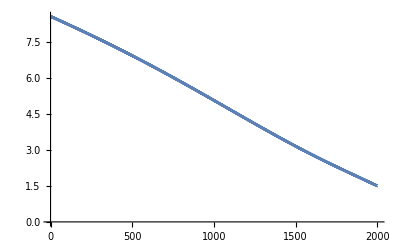

```mathematica
ListLinePlot[vv]
```